```mathematica
f=(1/(Sqrt[(1-o^2*l*c)^2+(o*r*c)^2]))
```

1/(√((1-c l o^2)^2+c^2 o^2 r^2))

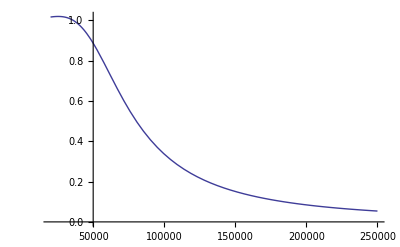

```mathematica
Plot[f/.l->(30/1000)/.r->(2.2*1000)/.c->(10/1000000000),{o,20000,250000}]
```

```mathematica
n=f/.o->0.2
```

1/(√((1-0.04 c l)^2+0.04 c^2 r^2))

```mathematica
Solve[{(f/.o->2.4n)==0.20,(f/.o->0n)==1,(f/.o->n)==2},{n,c,l,r}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{l→1.01632/(c n^2),r→-0.499733/(c n)},{l→-1.01632/(c n^2),r→-(0.+1.95335 ⅈ)/(c n)},{l→-1.01632/(c n^2),r→(0.+1.95335 ⅈ)/(c n)},{l→1.01632/(c n^2),r→0.499733/(c n)}}

```mathematica
1/(10/1000000000)
```

100000000

```mathematica
{(f/.o->0.2n)==1.04,(f/.o->1.2n)==1.34,(f/.o->2n)==0.32}
```

{1/(√((1-0.04 c l n^2)^2+0.04 c^2 n^2 r^2))==1.04,1/(√((1-1.44 c l n^2)^2+1.44 c^2 n^2 r^2))==1.34,1/(√((1-4 c l n^2)^2+4 c^2 n^2 r^2))==0.32}

```mathematica
o
```

```mathematica
Solve[{((1/(Sqrt[(1-o^2*l*c)^2+(o*r*c)^2]))/.o->0.2)==1.04,((1/(Sqrt[(1-o^2*l*c)^2+(o*r*c)^2]))/.o->0.4)==1.16,((1/(Sqrt[(1-o^2*l*c)^2+(o*r*c)^2]))/.o->0.6)==1.41},{l,r,c}]
```

{}

```mathematica
ClearAll[o]
```